# Mathematica 入門(2)

## ベクトル

#### ベクトルの内積，ノルム，なす角

```mathematica
{9,5,-2}.{1,1,1}
```

12

```mathematica
Norm[{9,5,-2}]
```

√110

```mathematica
Norm[{1,1,1}]
```

√3

なす角をθとするとCos[θ] は

```mathematica
{9,5,-2}.{1,1,1}/(Norm[{9,5,-2}]*Norm[{1,1,1}])
```

2 √(6/55)

```mathematica
N[{9,5,-2}.{1,1,1}/(Norm[{9,5,-2}]*Norm[{1,1,1}])]
```

0.660578

θの値は余弦関数の逆関数で求める．

```mathematica
N[ArcCos[{9,5,-2}.{1,1,1}/(Norm[{9,5,-2}]*Norm[{1,1,1}])]]
```

0.849208

```mathematica
N[Pi/4]
```

0.785398

### 空間ベクトルの外積

```mathematica
Cross[{9,5,-2},{1,1,1}]
```

{7,-11,4}

## パラメーター表示された図形の描画

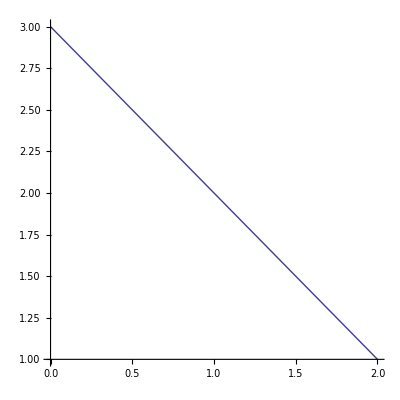

```mathematica
ParametricPlot[{1+t,2-t},{t,-1,1}]
```

```mathematica
{1+t-s, 2-2*t+s,3+t}
```

```mathematica
ParametricPlot3D[
{1+t-s, 2-2*t+s,3+t},
{t,-3,3},{s,-3,3}
]
```

-Graphics3D-

### 2 つの図形をひとつの空間 （または平面） 内に描画

```mathematica
ParametricPlot3D[
{1+t-s, 2-2*t+s,3+t},
{t,-3,3},{s,-3,3}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[
{1+2t, 2-t,2+t},
{t,-3,3}]
```

-Graphics3D-

```mathematica
Show[
ParametricPlot3D[
{1+t-s, 2-2*t+s,3+t},
{t,-3,3},{s,-3,3}],
ParametricPlot3D[
{1+2t, 2-t,2+t},
{t,-3,3}]
]
```

-Graphics3D-